# Pchem Assignment 5 – 7 November 2016

```mathematica
Directory[]
```

/Users/mlnance

```mathematica
tdnatall = Transpose[Import[ "/Users/mlnance/JHU_Class_Material/pchem/assignment_5/TDenat.xlsx","Data"]];
tdnat=Transpose[tdnatall[[2;;]]][[1]]
```

{{20.,384827.},{24.,378109.},{28.,368302.},{32.,351668.},{36.,337514.},{40.,313397.},{44.,268746.},{48.,178369.},{52.,81084.4},{56.,46140.6},{60.,36678.5},{64.,33935.7},{68.,29980.3},{72.,28432.7}}

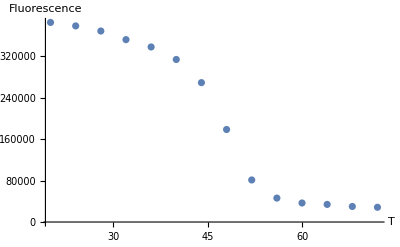

```mathematica
(*Plot the denaturation data*)
tdnatplot=ListPlot[tdnat,PlotRange->All,AxesLabel->{"T","Fluorescence"}]
```

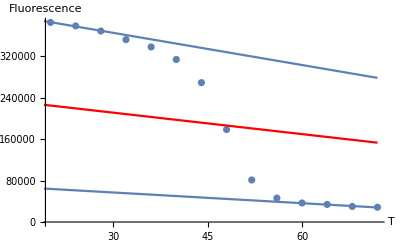

```mathematica
(*Fit the denaturation data to two baselines. Pick the first and last few points that would make linear baselines*) 
(*So Tm is around 48*)
ln=LinearModelFit[tdnat[[1;;3]],x,x];
fn[x_]:=ln["BestFitParameters"][[1]]+(ln["BestFitParameters"][[2]]*x);
lu=LinearModelFit[tdnat[[-3;;]],x,x];
fu[x_]:=lu["BestFitParameters"][[1]]+(lu["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lm=Table[ {x,((ln[x]-lu[x])/2)+lu[x]},{x,0,72}];
Show[tdnatplot,Plot[ln[x],{x,0,72}],Plot[lu[x],{x,0,72}],ListLinePlot[lm,PlotStyle->Red]]
```

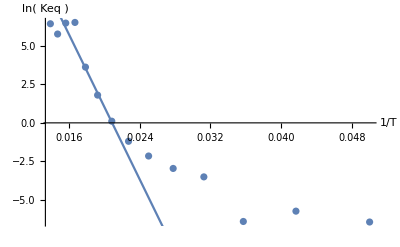

x-intercept = Tm = 47.9064

```mathematica
(*The x-intercept is the Tm. dG = 0 at Keq = 1 at Tm
dG = -RTln(Keq)
y = mx + b
ln(Keq) = ( -dG/R ) + (1/T)
*)
b=fn[tdnat[[All,1]]]-tdnat[[All,2]];
a=tdnat[[All,2]]-fu[tdnat[[All,1]]];
lnkvsintdata=Transpose[{(1/tdnat[[All,1]]),Re[Log[b/a]]}];
lnkvsinvt=ListPlot[lnkvsintdata];
lm2=LinearModelFit[lnkvsintdata[[-7;;-5]],x,x];
Show[lnkvsinvt,Plot[lm2[x],{x,Min[lnkvsintdata],Max[lnkvsintdata]}],AxesLabel->{"1/T","ln( Keq )"}]
(*y=mx+b --> ((y-b)/m)=x --> 1/((y-b)/m)=Tm*)
Print["x-intercept = Tm = ",tm =1/(( 0-lm2["BestFitParameters"][[1]])/lm2["BestFitParameters"][[2]])]
```

```mathematica
(*Doug's thing*)
(*part b then needs the b/a thing that gets Keq and then you get dG from that. Do dG vs x where the y-int is dgh20. Get dG by doing the dG = -RTln(k) equation*)
chemdenat1 = Transpose[Transpose[Import[ "/Users/mlnance/JHU_Class_Material/pchem/assignment_5/chemdenatdata1","Data"]][[3;;]]][[1]];
```

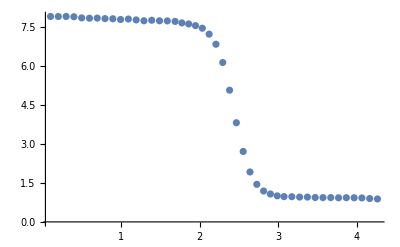

```mathematica
ListPlot[chemdenat1,PlotRange->All]
```